```mathematica
(** include the package proj2helpers which contains
Tons and MakePoints **)
Import["proj2helpers.m"];
```

```mathematica
(* 5 sizes *)
sizes = {10,25,50,250,1000};
(* let's assume 6 data points (secondss to compute) per size so
our data file should be 5 lines of 6 comma
separated numbers *)
fakedata = Import["faketimes.csv"];
TableForm[fakedata, TableHeadings->{sizes,{"foo","fee","foh","fum","fah","fal"}}];
```

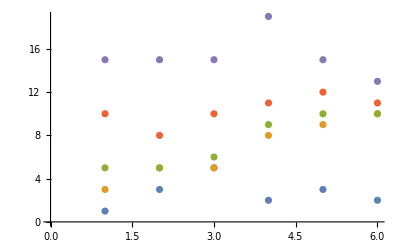

```mathematica
(* Just plotting times directly will associate the row/line 
  number with the x-coordinate.  We dont' want this because 
the sizes are not in fixed sized increments and if they were
the labels would be off *)
ListPlot[fakedata]
```

```mathematica
(* To solve this problem we need to transform the times into (size,time) pairs using MakePoints. *)
points = MakePoints[sizes,fakedata]
points[[1]]
points[[2]]
```

{{{10,1},{10,3},{10,5},{10,2},{10,3},{10,2}},{{25,3},{25,5},{25,5},{25,8},{25,9},{25,10}},{{50,5},{50,5},{50,6},{50,9},{50,10},{50,10}},{{250,10},{250,8},{250,10},{250,11},{250,12},{250,11}},{{1000,15},{1000,15},{1000,15},{1000,19},{1000,15},{1000,13}}}

{{10,1},{10,3},{10,5},{10,2},{10,3},{10,2}}

{{25,3},{25,5},{25,5},{25,8},{25,9},{25,10}}

```mathematica
(* Now I can Plot them with an accurately scaled x-axis *)
```

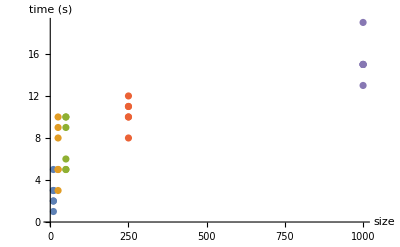

```mathematica
ListPlot[points,AxesLabel->{"size","time (s)"}]
```

```mathematica
(* To get pretty labels for the time units we need two things
Tons (To nanoseconds), which converts every entry in the table of
seconds to nanosecond units, and TimeUp which converts ns to whatever
the most appropriate unit of time is. TimeUp only works for one number
so we need to double map it (map to each row, then for each to each column).  This can
be done using anonymous functions like TimeUp[#] & *)
dataAsNS = Tons[fakedata]
TimeUp[#]&[dataAsNS[[1,1]]] 
Map[TimeUp[#]&,dataAsNS[[1]]]
(*timelabeleddata = Map[Map[TimeUp[#]&,#]&,Tons[fakedata]]*)
timelabeleddata = Map[Map[TimeUp,#]&,dataAsNS]
TableForm[timelabeleddata]
```

{{1000000000 ns,3000000000 ns,5000000000 ns,2000000000 ns,3000000000 ns,2000000000 ns},{3000000000 ns,5000000000 ns,5000000000 ns,8000000000 ns,9000000000 ns,10000000000 ns},{5000000000 ns,5000000000 ns,6000000000 ns,9000000000 ns,10000000000 ns,10000000000 ns},{10000000000 ns,8000000000 ns,10000000000 ns,11000000000 ns,12000000000 ns,11000000000 ns},{15000000000 ns,15000000000 ns,15000000000 ns,19000000000 ns,15000000000 ns,13000000000 ns}}

1 s

{1 s,3 s,5 s,2 s,3 s,2 s}

{{1 s,3 s,5 s,2 s,3 s,2 s},{3 s,5 s,5 s,8 s,9 s,10 s},{5 s,5 s,6 s,9 s,10 s,10 s},{10 s,8 s,10 s,11 s,12 s,11 s},{15 s,15 s,15 s,19 s,15 s,13 s}}

1 s | 3 s | 5 s | 2 s | 3 s | 2 s
3 s | 5 s | 5 s | 8 s | 9 s | 10 s
5 s | 5 s | 6 s | 9 s | 10 s | 10 s
10 s | 8 s | 10 s | 11 s | 12 s | 11 s
15 s | 15 s | 15 s | 19 s | 15 s | 13 s

```mathematica
isortdata = Import["isort.csv"];
isortSizes = isortdata[[1]]
isortTImes = isortdata[[2;;]]
```

{10,50,100,500,1000,5000,10000,25000,50000,75000,100000,150000,200000,250000}

{{1.151×10^-6,7.57×10^-7,8.85×10^-7,8.65×10^-7,6.89×10^-7,1.122×10^-6},{0.000013457,0.00001088,0.000012783,0.000013471,0.00001316,0.000024445},{0.00005096,0.000051897,0.000045889,0.000047275,0.000054884,0.000095854},{0.00130228,0.00123266,0.00123851,0.00135671,0.00129028,0.00283415},{0.00492524,0.00486351,0.00521621,0.00521698,0.00504129,0.0102084},{0.124653,0.123088,0.123711,0.126588,0.124672,0.253554},{0.496061,0.492277,0.49068,0.495056,0.512793,0.989746},{3.12139,3.13776,3.0913,3.13343,3.15965,6.19077},{12.4965,12.4572,12.5279,12.5007,12.5552,25.2716},{28.2093,28.2577,28.1188,28.566,27.9827,56.2592},{49.9449,49.7339,50.0696,50.0644,49.9368,99.4523},{112.37,112.207,111.876,111.625,111.77,221.199},{195.97,196.998,196.079,195.439,196.608,392.832},{306.965,299.804,298.864,297.738,298.081,595.631}}

```mathematica
Map[Map[Head,#]&,isortTImes] 
maxPerSize = Map[Max,isortTImes];
TableForm[maxPerSize];
isorttimeNS  = Tons[isortTImes];
TableForm[Map[TimeUp,Map[Max,isorttimeNS]]]
```

{{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real}}

1.151 µs
24.445 µs
95.854 µs
2.83415 ms
10.2084 ms
253.554 ms
989.746 ms
6.19077 s
25.2716 s
56.2592 s
1.65754 min
3.68665 min
6.5472 min
9.92718 min

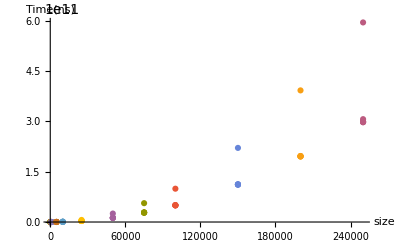

```mathematica
isortPoints = MakePoints[isortSizes,isorttimeNS];
isortgraph = ListPlot[isortPoints,PlotRange->All,AxesLabel->{"size","Time(ns)"}]
```

```mathematica
Export["isortpoints.png",isortgraph, ImageSize -> Large]
```

isortpoints.png